```mathematica
(* set-up *)
vec1[A1_,A2_]:=-(M0*A1+K0*A1^3+K1*A1*A2^2)
vec2[A1_,A2_]:=-(M0*A2+K0*A2^3+K1*A2*A1^2)
```

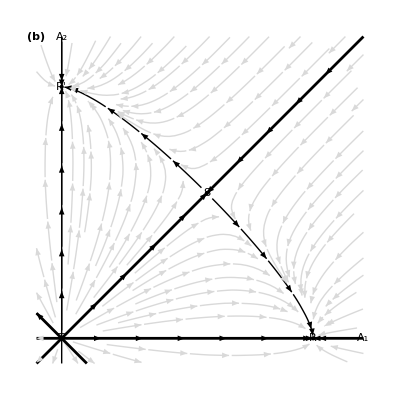

```mathematica
(* plot for M0 < 0, K0 > 0, K0 + K1 > 0 and K1 - K0 > 0 *)
M0=-1;
K0=1;
K1=2;
rolls={Sqrt[-M0/K0],0};
rollsY={0,Sqrt[-M0/K0]};
square={Sqrt[-M0/(K0+K1)],Sqrt[-M0/(K0+K1)]};
lineStyle={Thick};
line1=Line[{{0,-0.1},{0,1.2}}];
fig=Plot[{x,0},{x,-0.1,1.2},PlotStyle->Black,Ticks->None];
fig2=Plot[-x,{x,-0.1,0.1},PlotStyle->Black,Ticks->None];
vecfield=StreamPlot[{-(M0*A1+K0*A1^3+K1*A1*A2^2),-(M0*A2+K0*A2^3+K1*A2*A1^2)},{A1,-0.1,1.2},{A2,-0.1,1.2},Epilog->{Black,PointSize[Large],Point[{rolls,{0,0},square,rollsY}],
Text[Style[" R ",Italic,Larger],rolls,{0,2},Background->White],Text[Style[" T ",Italic,Larger],{0,0},{1.5,2},Background->White],
Text[Style[" S ",Italic,Larger],square,{0,-2},Background->White],Text[Style[" (b) ",Bold,Larger],{-0.1,1.2},{-1,2},Background->White],
Text[Style[" R' ",Italic,Larger],rollsY,{1.5,0},Background->White],
Text[Style["A_1",Italic,Larger],{1.2,0},{0,-1.5},Background->White],
Text[Style["A_2",Italic,Larger],{0,1.2},{-1.5,0},Background->White],
Directive[lineStyle],line1},
StreamColorFunction->None,
StreamStyle->LightGray,
StreamScale->0.12,
StreamPoints->{{{{0.2,0},Black},
			{{1.1,0},Black},
			{{0.2,0.2},Black},
			{{1,1},Black},
			{{-0.1,0.1},Black},
			{{0.8,0.33459},Black},
			{{0,0.1},Black},
			{{0,1.1},Black},
			{{0.33459,0.8},Black},
			Automatic}},
FrameTicks->None,Frame->False];
figure=Show[vecfield,fig,fig2]
```

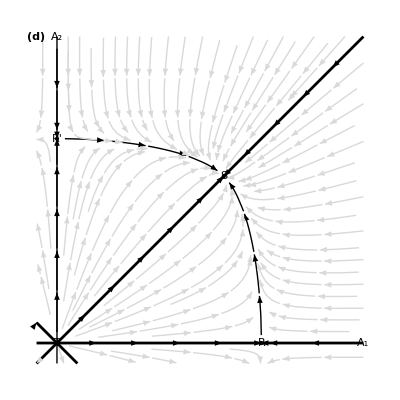

```mathematica
(* plot for M0 < 0, K0 > 0, K0 + K1 < 0 and K1 - K0 > 0 *)
M0=-1;
K0=1;
K1=0.5;
rolls={Sqrt[-M0/K0],0};
square={Sqrt[-M0/(K0+K1)],Sqrt[-M0/(K0+K1)]};
rollsY={0,Sqrt[-M0/K0]};
lineStyle={Thick};
line1=Line[{{0,-0.1},{0,1.5}}];
fig=Plot[{x,0},{x,-0.1,1.5},PlotStyle->Black,Ticks->None];
fig2=Plot[-x,{x,-0.1,0.1},PlotStyle->Black,Ticks->None];
vecfield=StreamPlot[{-(M0*A1+K0*A1^3+K1*A1*A2^2),-(M0*A2+K0*A2^3+K1*A2*A1^2)},{A1,-0.1,1.5},{A2,-0.1,1.5},Epilog->{Black,PointSize[Large],Point[{rolls,{0,0},square,rollsY}],
Text[Style[" R ",Italic,Larger],rolls,{0,2},Background->White],Text[Style[" T ",Italic,Larger],{0,0},{1.5,2},Background->White],
Text[Style[" S ",Italic,Larger],square,{0,-2},Background->White],Text[Style[" (d) ",Bold,Larger],{-0.1,1.5},{-0.5,2},Background->White],
Text[Style[" R' ",Italic,Larger],rollsY,{1.5,0},Background->White],
Text[Style["A_1",Italic,Larger],{1.5,0},{0,-1.5},Background->White],
Text[Style["A_2",Italic,Larger],{0,1.5},{-1.5,0},Background->White],
Directive[lineStyle],line1},
StreamColorFunction->None,
StreamStyle->LightGray,
StreamScale->0.12,
StreamPoints->{{{{0.2,0},Black},
			{{1.1,0},Black},
			{{0.2,0.2},Black},
			{{1,1},Black},
			{{-0.1,0.1},Black},
			{{0,0.2},Black},
			{{0,1.1},Black},
			{rolls+0.04*{0,1},Black},
			{rollsY+0.04*{1,0},Black},
			Automatic}},
FrameTicks->None,Frame->False];
figure=Show[vecfield,fig,fig2]
```

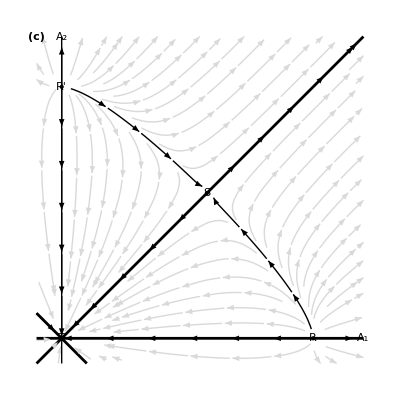

```mathematica
(* plot for M0 > 0, K0 < 0, K0 + K1 < 0 and K1 - K0 < 0 *)
M0=1;
K0=-1;
K1=-2;
rolls={Sqrt[-M0/K0],0};
rollsY={0,Sqrt[-M0/K0]};
square={Sqrt[-M0/(K0+K1)],Sqrt[-M0/(K0+K1)]};
lineStyle={Thick};
line1=Line[{{0,-0.1},{0,1.2}}];
fig=Plot[{x,0},{x,-0.1,1.2},PlotStyle->Black,Ticks->None];
fig2=Plot[-x,{x,-0.1,0.1},PlotStyle->Black,Ticks->None];
vecfield=StreamPlot[{-(M0*A1+K0*A1^3+K1*A1*A2^2),-(M0*A2+K0*A2^3+K1*A2*A1^2)},{A1,-0.1,1.2},{A2,-0.1,1.2},Epilog->{Black,PointSize[Large],Point[{rolls,{0,0},square,rollsY}],
Text[Style[" R ",Italic,Larger],rolls,{0,2},Background->White],Text[Style[" T ",Italic,Larger],{0,0},{1.5,2},Background->White],
Text[Style[" S ",Italic,Larger],square,{0,-2.5},Background->White],Text[Style[" (c) ",Bold,Larger],{-0.1,1.2},{-1,2},Background->White],
Text[Style[" R' ",Italic,Larger],rollsY,{1.5,0},Background->White],
Text[Style["A_1",Italic,Larger],{1.2,0},{0,-1.5},Background->White],
Text[Style["A_2",Italic,Larger],{0,1.2},{-1.5,0},Background->White],
Directive[lineStyle],line1},
StreamColorFunction->None,
StreamStyle->LightGray,
StreamScale->0.12,
StreamPoints->{{{{0.2,0},Black},
			{{1.1,0},Black},
			{{0,0.2},Black},
			{{0,1.1},Black},
			{{0.2,0.2},Black},
			{{1,1},Black},
			{{-0.1,0.1},Black},
			{{0.8,0.33499},Black},
			{{0.33499,0.8},Black},
			Automatic}},
FrameTicks->None,Frame->False];
figure=Show[vecfield,fig,fig2]
```

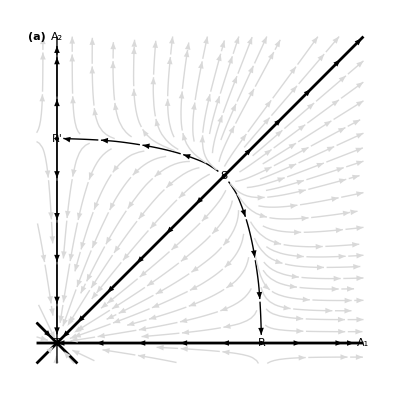

```mathematica
(* plot for M0 < 0, K0 > 0, K0 + K1 < 0 and K1 - K0 > 0 *)
M0=1;
K0=-1;
K1=-0.5;
rolls={Sqrt[-M0/K0],0};
rollsY={0,Sqrt[-M0/K0]};
square={Sqrt[-M0/(K0+K1)],Sqrt[-M0/(K0+K1)]};
lineStyle={Thick};
line1=Line[{{0,-0.1},{0,1.5}}];
fig=Plot[{x,0},{x,-0.1,1.5},PlotStyle->Black,Ticks->None];
fig2=Plot[-x,{x,-0.1,0.1},PlotStyle->Black,Ticks->None];
vecfield=StreamPlot[{-(M0*A1+K0*A1^3+K1*A1*A2^2),-(M0*A2+K0*A2^3+K1*A2*A1^2)},{A1,-0.1,1.5},{A2,-0.1,1.5},Epilog->{Black,PointSize[Large],Point[{rolls,{0,0},square,rollsY}],
Text[Style[" R ",Italic,Larger],rolls,{0,2},Background->White],Text[Style[" T ",Italic,Larger],{0,0},{1.5,2},Background->White],
Text[Style[" S ",Italic,Larger],square,{0,-2},Background->White],Text[Style[" (a) ",Bold,Larger],{-0.1,1.5},{-0.5,2},Background->White],
Text[Style[" R' ",Italic,Larger],rollsY,{1.5,0},Background->White],
Text[Style["A_1",Italic,Larger],{1.5,0},{0,-1.5},Background->White],
Text[Style["A_2",Italic,Larger],{0,1.5},{-1.5,0},Background->White],
Directive[lineStyle],line1},
StreamColorFunction->None,
StreamStyle->LightGray,
StreamScale->0.12,
StreamPoints->{{{{0.2,0},Black},
			{{1.1,0},Black},
			{{0,0.2},Black},
			{{0,1.1},Black},
			{{0.2,0.2},Black},
			{{1,1},Black},
			{{-0.1,0.1},Black},
			{rolls+0.04*{0,1},Black},
			{rollsY+0.04*{1,0},Black},
			Automatic}},
FrameTicks->None,Frame->False];
figure=Show[vecfield,fig,fig2]
```